# Estimating the limits of detection for NCR assay

The goal here is to estimate a lower bound on the detection limit of NCR using a simplified model of the
critical catalytic reactions that happen in the first seconds of the NCR reaction. Here we focus on the exponential phase of growth that will take
place in early steps before a significant fraction of caged activator is exhausted (at which point growth rate will start to depend on time)

```mathematica
Clear["Global`*"]
```

## Key Assumptions

(1) Neglecting noise from stochastic binding and unbinding reactions
(2) I that pre-mixing of RNPs ensures that Cas13 and guide are in equilibrium wrpt other reactants
(3) Assume equivalent Kd (“KdNS”) for all non-specific interactions (i.e. all interactions not between Cas13, its guide, and its target)

## Calculate the expected initial concentration of bound cage

#### (1) Pre-equilibrated RNP solutions

```mathematica
solG1 = Solve[{(RNP1-G1)*rcg==k*G1^2},G1];
```

```mathematica
G10 = G1/.solG1[[1]];
```

```mathematica
CG10 = FullSimplify[RNP1-G10];
```

```mathematica
solG2 = Solve[{(RNP2-G2)*rcg==k*G2^2},G2];
```

```mathematica
G20 = G2/.solG2[[1]];
```

```mathematica
CG20 = FullSimplify[RNP2-G20];
```

#### (2) Calculate fraction of primary activator (activator 1/viralRNA) bound to Cas13-Guide complex (accounting for competition from free guide) Assume that viral concentration is substantially lower than [RNP]. Neglect competition from off-target binding partners

```mathematica
solCG1A1 = Solve[{CG1A1==CG10*A10/(rga/k+CG10+G10)},CG1A1];
CG1A10 = FullSimplify[CG1A1/.solCG1A1[[1]]];
```

```mathematica
solG1A1 = Solve[{G1A1==G10*A10/(rga/k+CG10+G10)},G1A1];
G1A10 = FullSimplify[G1A1/.solG1A1[[1]]];
```

(A10 (-rcg+√rcg √(rcg+4 k RNP1)))/(2 (rga+k RNP1))

```mathematica
solCG2A2 = Solve[{CG2A2==CG20*A2T/(rga/k+CG20+G20)},CG2A2];
CG2A20 = FullSimplify[CG2A2/.solCG2A2[[1]]];
```

```mathematica
solG2A2 = Solve[{G2A2==G20*A2T/(rga/k+CG20+G20)},G2A2];
G2A20 = FullSimplify[G2A2/.solG2A2[[1]]];
```

```mathematica
A20 = FullSimplify[A2T-CG2A20 -G2A20 ];
```

#### (3) Calculate amount of caged activator by Active and inactive Cas13 complex, accounting for off-target binding This dictates the effective initial catalytic rate. Assume that CG20 can effectively be treated as invariant

```mathematica
eqCG1A1S = 0 == k*S*CG1A1-rns*CG1A1S;
```

```mathematica
eqCG1A1= 0 == CG1A1T-CG1A1S-CG1A1;
```

```mathematica
eqCG2A2S = 0 == k*S*CG2A2-rns*CG2A2S;
```

```mathematica
eqCG2A2= 0 == CG2A2T-CG2A2S-CG2A2;
```

```mathematica
eqCG1S = 0 == k*S*CG1-rns*CG1S;
```

```mathematica
eqCG1= 0 == CG1T-CG1S-CG1;
```

```mathematica
eqCG2S = 0 == k*S*CG2-rns*CG2S;
```

```mathematica
eqCG2= 0 == CG2T-CG2S-CG2;
```

```mathematica
eqBS = 0== k*B*S - rns*BS;
```

```mathematica
eqB = 0==B0-BS-B;
```

```mathematica
consVec = {CG1A1-> CG1A1T-CG1A1S,CG2A2-> CG2A2T-CG2A2S,CG1-> CG1T-CG1S,CG2-> CG2T-CG2S,B->B0-BS,S->S0-CG1A1S-CG2A2S-CG1S-CG2S-BS};
```

```mathematica
eqSys = {eqCG1A1S,eqCG2A2S,eqCG1S ,eqCG2S,eqBS }/.consVec;
```

```mathematica
sol = Solve[eqSys,{CG1S,CG2S,CG1A1S,CG2A2S,BS}];
```

#### (4) Extract quantities of interest and run some sanity checks on their behavior

```mathematica
CG1A1Ssol =FullSimplify[CG1A1S/.sol[[1]]] /.{CG1T->CG10,CG2T->CG20,CG1A1T->CG1A10,CG2A2T->CG2A20};
```

```mathematica
CG1Ssol = FullSimplify[CG1S/.sol[[1]] ]/.{CG1T->CG10,CG2T->CG20,CG1A1T->0,CG2A2T->0};
```

```mathematica
CG2A2Ssol = FullSimplify[CG2A2S/.sol[[1]] ]/.{CG1T->CG10,CG2T->CG20,CG1A1T->CG1A10,CG2A2T->CG2A20};
CG2Ssol = FullSimplify[CG2S/.sol[[1]] ]/.{CG1T->CG10,CG2T->CG20,CG1A1T->0,CG2A2T->0};
```

```mathematica
valVec = {k->1,rs->1,B0->0,A2T->0,A10->1,S0->200,RNP1->20,RNP2->1};
```

```mathematica
CG1A1Sval[k_] = CG1A1Ssol /.{A10->1,rga->0.001,rcg->.1,B0->10000,rns->2000,RNP2->1,RNP1->20,S0->200,A2T->1};
```

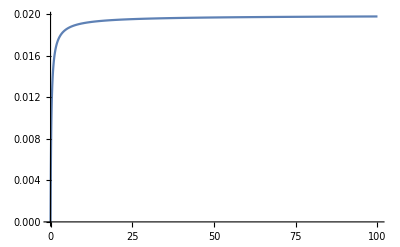

```mathematica
Plot[CG1A1Sval[k],{k,0,100},PlotRange->All]
```

## Calculate approximate expected mean and variance for Positive Sample and Null Control

#### Define standard quantities needed for diff calculation

```mathematica
keff = kc*CG2A20/A2T;
```

```mathematica
muP0 = ((C1S+C2S)*bc+A1S+wc);
```

```mathematica
sigmaP0 = Sqrt[((C1S+C2S)*bc+A1S+wc)];
```

```mathematica
muN0 = ((C1S+C2S)*bc+wc);
```

```mathematica
sigmaN0 = Sqrt[((C1S+C2S)*bc+wc)];
```

```mathematica
muDelta = FullSimplify[muP0-muN0];
```

```mathematica
eqD1 = muDelta == 2*(sigmaP0+sigmaN0);
```

#### Apply simplifying assumptions and solve for A10

```mathematica
staticVals = {S0->200*10^11,k->10^8,rcg->10^8,rns->10^11,wc->10^-10,kc->200,A2T->0};
```

```mathematica
vals = {RNP1->60*10^9,RNP2->6*10^9,B0->10^13,bc->10^-4,rga->10^8};
```

```mathematica
eqD1Full = N[eqD1/.{C1S->CG1Ssol,C2S->CG2Ssol,A1S->CG1A1Ssol,wc->wc*keff/kc} /.staticVals];
```

```mathematica
FullSimplify[N[CG1Ssol /.staticVals]];
```

```mathematica
expOut = 2*(sigmaP0+sigmaN0)- muDelta /.{C1S->CG1Ssol,C2S->CG2Ssol,A1S->CG1A1Ssol,wc->wc*keff/kc} /.A2T->0
```

$Aborted

```mathematica
A1Ssol = A1s/.ASsol[[1]];
```

```mathematica
<<ToMatlab`
```

```mathematica
eqD1Full//ToMatlab
```